```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals,ν>0};
```

```mathematica
e[x_]:=ν{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν ψ'[x]}}

```mathematica
b[x_]:={{-ν ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν)

```mathematica
H[x_]:=-ψ'[x]/(2 ν)
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+ H''[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν^2 σ[x] ψ'[x]==κ (ψ'[x]^3+2 ν^2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν Cos[ψ[x]],X2'[x]==-ν Sin[ψ[x]]}
```

{X1'[x]==ν Cos[ψ[x]],X2'[x]==-ν Sin[ψ[x]]}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,X1[xmin]==X1min,X2[xmin]==X2min,X1[xmax]==X1max};
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=0;
xmax=1;
ψmin=-1/2;
ψmax=2.5;
X1min=0;
X2min=0;
X1max=1;
```

```mathematica
ν=8;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,bcs}],{ψ,X1,X2},{x,xmin,xmax}]
```

{{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}}

```mathematica
X2[xmax]/.s
```

{-2.39568}

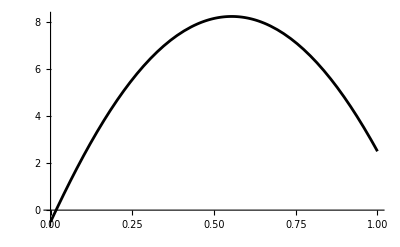

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Black]
```

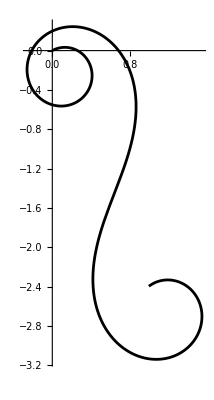

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Black]
```